```mathematica
NALOGA 1
```

```mathematica
ClearAll[daljica, Dolzina, EnacbaNosilke]
```

```mathematica
Daljica[{AA_, BB_}]:= {{x,y}, {x1, y1}}
```

```mathematica
daljica=Daljica[{-1, 1}, {3,-1}]
```

Daljica[{-1,1},{3,-1}]

```mathematica
Dolzina[Daljica[AA_, BB_]]:=Norm[AA-BB]
Dolzina[daljica]
```

2 √5

```mathematica
ClearAll[x,y,EnacbaNosilke]
EnacbaNosilke[Daljica[AA_,BB_]]:= Module[{x1,y1,x2,y2,k,n},
{x1,y1}=AA;
 {x2,y2}=BB;
 k=(y2-y1)/(x2-x1);
 n=n/.First[Solve[y1==k*x1+n, n]];
y==k*x+n
]
```

```mathematica
EnacbaNosilke[daljica]
```

y==1/2-x/2

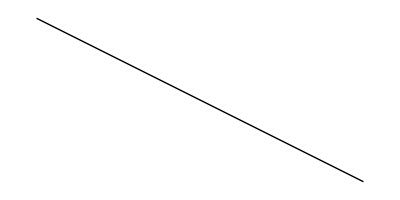

```mathematica
Graphics[Line[{{-1, 1}, {3,-1}}]]
```

```mathematica
a:=Daljica[AA_, BB_]
b:=Daljica[CC_, DD_]
```

```mathematica
Presek[a_,b_]:= {x,y}/.First[Solve
```